output signal

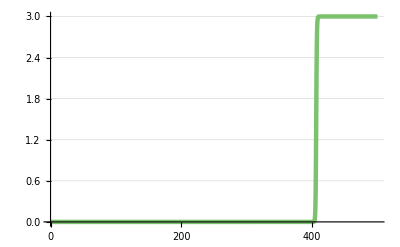

helper species

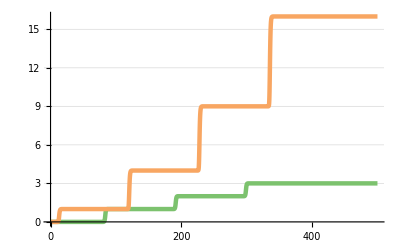

```mathematica
Get[NotebookDirectory[]<>"/intSqrt.m"]
rsys=IntSqrtRsys[10];
tmax=500;
sol=SimulateRxnsys[ExpandDiscreteRsys[crn], tmax];
Print["output signal"];
PlotForPaper[Evaluate[{out[t]}/.sol], tmax]
Print["helper species"];
PlotForPaper[Evaluate[{z[t],zpow[t]}/.sol], tmax]
```